CVTPulley — Reproduce convergence table near t = 0.5

This notebook reproduces the supplementary convergence table reporting the
number of iterations required to reach the stopping tolerance near t = 0.5.

The table is intended to complement the convergence discussion in the article
by providing a compact quantitative illustration of the mild slowdown of the
symmetrization procedure in the vicinity of the midpoint.

Before using this notebook, evaluate 00_LoadProject.nb so that the package
is loaded.

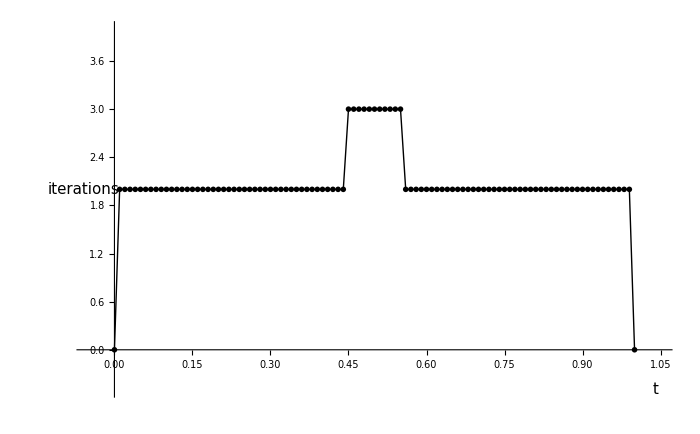

```mathematica
(* ::Section::*)
(*Convergence rate near t=0.5*)

params0=CVTPulley`TypesAndValidation`MakeParameters[<|"rMin"->10,"rMax"->30,"d"->70,"nGrid"->100,"epsBis"->10^-12,"epsSym"->10^-6,"workingPrecision"->30,"exportBaseName"->"convergence_near_half"|>];

params=CVTPulley`BeltLength`SetReferenceBeltLength[params0];

symDataConv=CVTPulley`Symmetrization`SymmetrizationData[params,"StoreHistory"->False,"ImplicitStoreHistory"->False];

nConv=params["nGrid"];
tGridConv=N[Range[0,nConv]/nConv];
iterCountsConv=ConstantArray[Indeterminate,nConv+1];

Do[Module[{res,i,j},res=symDataConv["PairResults"][[k]];
i=res["PairIndexLeft"];
j=res["PairIndexRight"];
iterCountsConv[[i+1]]=res["IterationsPerformed"];
iterCountsConv[[j+1]]=res["IterationsPerformed"];],{k,Length[symDataConv["PairResults"]]}];

If[AssociationQ[symDataConv["MidpointResult"]],iterCountsConv[[symDataConv["MidpointResult","Index"]+1]]=symDataConv["MidpointResult","IterationsPerformed"];];

convData=Transpose[{tGridConv,iterCountsConv}];
yMaxConv=Max[DeleteCases[iterCountsConv,Indeterminate]];

figConvNearHalf=Show[{ListLinePlot[convData,PlotStyle->Directive[Black,AbsoluteThickness[1.0]],InterpolationOrder->1],ListPlot[convData,PlotStyle->Directive[Black],PlotMarkers->{Automatic,0.012},Joined->False]},Axes->True,Frame->False,AxesOrigin->{0,0},AxesStyle->Directive[Black,AbsoluteThickness[0.8]],TicksStyle->Directive[Black,12],PlotRange->{{-0.05,1.05},{-0.5,yMaxConv+1}},PlotRangePadding->Scaled[0.02],ImageSize->700,AspectRatio->0.62,Epilog->{Inset[Style["t",15,Black,Italic],{1.04,-0.5}],Rotate[Inset[Style["iterations",15,Black],{-0.06,(yMaxConv+1)/2}],Pi/2]}];

figConvNearHalf
```

```mathematica
(* ::Section::*)
(*Supplementary convergence table near t=0.5*)

params0=CVTPulley`TypesAndValidation`MakeParameters[<|"rMin"->10,"rMax"->30,"d"->70,"nGrid"->100,"epsBis"->10^-12,"epsSym"->10^-6,"workingPrecision"->30,"exportBaseName"->"convergence_near_half"|>];

params=CVTPulley`BeltLength`SetReferenceBeltLength[params0];

tValsConv={0.40,0.43,0.46,0.48, 0.49, 0.495, 0.499, 0.5};
iValsConv=Round[100 tValsConv];

iterCountsConv=Table[If[i==50,CVTPulley`Symmetrization`IterateMidpoint[params,"StoreHistory"->False,"ImplicitStoreHistory"->False]["IterationsPerformed"],CVTPulley`Symmetrization`IterateSymmetricPair[i,params,"StoreHistory"->False,"ImplicitStoreHistory"->False]["IterationsPerformed"]],{i,iValsConv}];

convTableHeader=Map[Style[NumberForm[#,{4,3}],14]&,tValsConv];

convTableBody=Map[Style[#,14]&,iterCountsConv];

Column[{Grid[{Prepend[convTableHeader,Style[Subscript[Style["t",Italic],"i"],16]],Prepend[convTableBody,Style["iterations",16]]},Frame->All,Spacings->{1.2,1.0},Alignment->Center,BaseStyle->{FontSize->14}],Style["Supplementary table: number of iterations required to reach the stopping tolerance near t = 0.5.",14]},Spacings->1.2]
```

t_i | 0.400 | 0.430 | 0.460 | 0.480 | 0.490 | 0.495 | 0.499 | 0.500
iterations | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3
Supplementary table: number of iterations required to reach the stopping tolerance near t = 0.5.